# Exploratory plots

```mathematica
ClearAll["Global`*"];
```

```mathematica
ϕ={ϕ1, I ϕ3};
m=10;λ=1;V=-m^2/2 ϕ.ϕ+λ/4(ϕ.ϕ)^2
```

-50 (ϕ1^2-ϕ3^2)+1/4 (ϕ1^2-ϕ3^2)^2

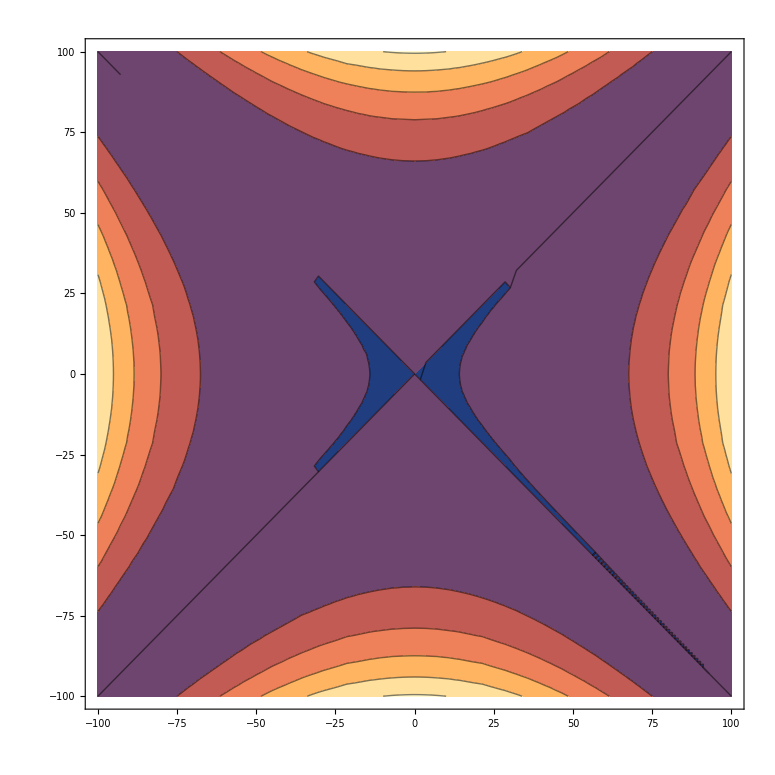

```mathematica
ContourPlot[V,{ϕ1,-100,100},{ϕ3,-100,100}]
```

```mathematica
Clear[ϕ1, ϕ3];
ϕ={ϕ1, ϕ3};
m=15;λ=1;V=-m^2/2 ϕ.ϕ+λ/4(ϕ.ϕ)^2;
Print[Plot3D[V,{ϕ1,-20,20},{ϕ3,-20,20}]];
```

-Graphics3D-

```mathematica
ϕ={ϕ1,I ϕ3};
m=15;λ=1;V=m^2/2 ϕ.ϕ+λ/4(ϕ.ϕ)^2;
Print[Plot3D[V,{ϕ1,-40,40},{ϕ3,-40,40}]];
```

-Graphics3D-

```mathematica
ϕ1=f Sinh[x];ϕ3=f Cosh[x];
FullSimplify[ϕ.ϕ]
```

-f^2

```mathematica
Sin[I x]
```

ⅈ Sinh[x]

```mathematica
Cos[I x]
```

Cosh[x]

```mathematica
Π->I Π
```

```mathematica
Cot[I Π/f]
```

-ⅈ Coth[Π/10]

```mathematica
Clear[f]
```

# Gegenbauer equation

```mathematica
ClearAll["Global`*"]
```

```mathematica
DSolve[{G''[x]+2λ Cot[x]G'[x]+cc G[x]==0},G[x],x]
```

{{G[x]→C[1] (-1+Cos[x]^2)^(1/4 (1-2 λ)) LegendreP[1/2 (-1+2 √(cc+λ^2)),1/2 (-1+2 λ),Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4 (1-2 λ)) LegendreQ[1/2 (-1+2 √(cc+λ^2)),1/2 (-1+2 λ),Cos[x]]}}

```mathematica
DSolve[{G''[x]+2λ Cot[x]G'[x]+n(n+2λ)G[x]==0},G[x],x]
```

{{G[x]→C[1] (-1+Cos[x]^2)^(1/4 (1-2 λ)) LegendreP[1/2 (-1+2 n+2 λ),1/2 (-1+2 λ),Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4 (1-2 λ)) LegendreQ[1/2 (-1+2 n+2 λ),1/2 (-1+2 λ),Cos[x]]}}

```mathematica
NN=4;n=21;λ=(NN-1)/2;sol=DSolve[{G''[x]+2λ Cot[x]G'[x]+n(n+2λ)G[x]==0},G[x],x];
```

```mathematica
Gegenbauer1[xx_?NumericQ]:=(G[x]/.(sol[[1]]/.{C[2]->0,C[1]->1}))/.{x->xx};Gegenbauer2[xx_?NumericQ]:=(G[x]/.(sol[[1]]/.{C[2]->1,C[1]->0}))/.{x->xx};
```

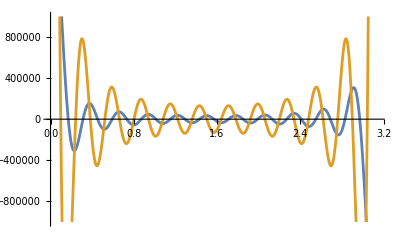

```mathematica
Plot[{10^11 Gegenbauer1[x],Gegenbauer2[x]},{x,0,π},PlotRange->{-10^6,10^6}]
```

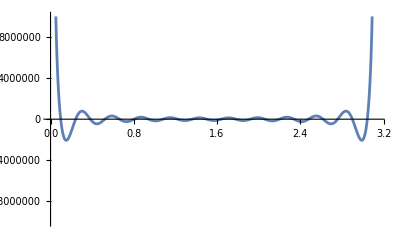
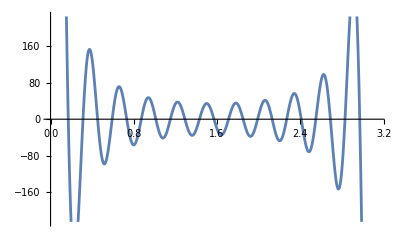

```mathematica
{Plot[Gegenbauer2[x],{x,0,π},PlotRange->{-10^7,10^7}],Plot[10^8Gegenbauer1[x],{x,0,π}]}
```

```mathematica
Plot[Gegenbauer2[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
G''[x]+2λ Cot[x]G'[x]+n(n+2λ)G[x]
```

```mathematica
Clear[λ]
```

```mathematica
Gansatz[Π_]:=GegenbauerC[nG,λ,Cos[Π]]
```

```mathematica
Gansatz''[x]
```

-2 λ Cos[x] GegenbauerC[-1+nG,1+λ,Cos[x]]+4 λ (1+λ) GegenbauerC[-2+nG,2+λ,Cos[x]] Sin[x]^2

```mathematica
FullSimplify[Gansatz''[x]+2λ Cot[x]Gansatz'[x]+nG(nG+2λ)Gansatz[x]]
```

-2 λ (1+2 λ) Cos[x] GegenbauerC[-1+nG,1+λ,Cos[x]]+nG (nG+2 λ) GegenbauerC[nG,λ,Cos[x]]+4 λ (1+λ) GegenbauerC[-2+nG,2+λ,Cos[x]] Sin[x]^2

```mathematica
Clear[λ,nG];
λ=3/2;nG=40;
```

```mathematica
FullSimplify[Gansatz''[x]+2λ Cot[x]Gansatz'[x]+nG(nG+2λ)Gansatz[x]]
```

0

# Gegenbauer paper

```mathematica
ClearAll["Global`*"]
```

```mathematica
Npi=2;(*Number of Goldstones!!*)
pivec=Table[pi[i],{i,1,Npi}];
Pinorm=√(pivec.pivec);
gmetric=Sin[Pinorm/f]^2 f^2/Pinorm^2 Table[KroneckerDelta[a,b]+pi[a]pi[b]/Pinorm^2((Pinorm^2/f^2)Csc[Pinorm/f]^2-1),{a,1,Npi},{b,Npi}];
gmetricinverse=1/(Sin[Pinorm/f]^2) Pinorm^2 /f^2Table[KroneckerDelta[a,b]-pi[a]pi[b]/Pinorm^2(1-f^2/Pinorm^2 Sin[Pinorm/f]^2),{a,1,Npi},{b,Npi}];
Print["Check g times g^-1"]
Print[MatrixForm[FullSimplify[gmetric.gmetricinverse]]];
dgilk=Hold[Sum[gmetricinverse[[i,m]](D[gmetric[[l,m]],pi[k]]+D[gmetric[[k,m]],pi[l]]-D[gmetric[[l,k]],pi[m]]),{m,1,Npi}]];Christoffel=1/2Table[ReleaseHold[dgilk],{i,1,Npi},{l,1,Npi},{k,1,Npi}];
Potential=G[Pinorm];
gD2V=Hold[Sum[gmetricinverse[[i,k]]D[Potential,pi[k],pi[j]],{k,1,Npi}]];
gGamDV=Hold[Sum[gmetricinverse[[i,l]] Christoffel[[m,j,l]]D[Potential,pi[m]],{m,1,Npi},{l,1,Npi}]];MassMatrix=Table[ReleaseHold[gD2V-gGamDV],{i,1,Npi},{j,1,Npi}];
```

Check g times g^-1

(1 | 0
0 | 1)

```mathematica
(*Γ=FullSimplify[Christoffel/.Table[pi[i]->0,{i,2,Npi}]/.{pi[1]->Π}];
ginv=FullSimplify[gmetricinverse/.Table[pi[i]->0,{i,2,Npi}]/.{pi[1]->Π}];
MatrixForm[FullSimplify[ginv.{{xx,0},{0,0}}-ginv.(Γ.{y,0})]]*)
```

```mathematica
Riemantensor[α_,β_,γ_,δ_]:=Hold[D[Christoffel[[α,β,δ]],pi[γ]]-D[Christoffel[[α,β,γ]],pi[δ]]+Sum[Christoffel[[μ,β,δ]]Christoffel[[α,μ,γ]]-Christoffel[[μ,β,γ]]Christoffel[[α,μ,δ]],{μ,1,Npi}]];
RiemantensorMatrix=Table[ReleaseHold[Riemantensor[α,β,γ,δ]],{α,1,Npi},{β,1,Npi},{γ,1,Npi},{δ,1,Npi}];RicciCurvatureTensor=Hold[Sum[RiemantensorMatrix[[λ]][[μ]][[λ]][[κ]],{λ,1,Npi}]];
RicciCurvatureTensorMatrix=Table[ReleaseHold[RicciCurvatureTensor],{μ,1,Npi},{κ,1,Npi}];CurvatureScalar=FullSimplify[Tr[gmetricinverse.RicciCurvatureTensorMatrix]];
```

```mathematica
CurvatureScalar
```

2/f^2

```mathematica
Replace[ FullSimplify[Tr[MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(-F^2+Sum[pi[i]^2,{i,1,Npi}])->-F^2+Π^2,Sum[pi[i]^2,{i,1,Npi}]->Π^2},All]
```

(Cot[(√(Π^2))/f] G'[√(Π^2)])/f+G''[√(Π^2)]

```mathematica
EigenMasses=FullSimplify[Replace[MassMatrix/.Table[pi[i]->0,{i,2,Npi}],{pi[1]->Π},All]];EigenMasses
```

{{G''[√(Π^2)],0},{0,(Cot[(√(Π^2))/f] G'[√(Π^2)])/f}}

```mathematica
MatrixForm[EigenMasses]
```

(G''[√(Π^2)] | 0
0 | (Cot[(√(Π^2))/f] G'[√(Π^2)])/f)

```mathematica
pivecST=Table[Dpi[i],{i,1,Npi}];
index=1;
EOMindex=Sum[Christoffel[[index,j,k]]pivecST[[j]]pivecST[[k]] ,{j,1,Npi},{k,1,Npi}]-Sum[D[Potential,pi[j]]gmetricinverse[[index,j]],{j,1,Npi}];FullSimplify[Replace[EOMindex/.Join[Table[pi[i]->0,{i,2,Npi}],Table[Dpi[i]->0,{i,2,Npi}]],{pi[1]->Π,Dpi[1]->Π'},All],Π>0]
```

-G'[Π]

```mathematica
FullSimplify[Det[gmetricinverse]]
```

(Csc[(√(pi[1]^2+pi[2]^2))/f]^2 (pi[1]^2+pi[2]^2))/f^2

```mathematica
Replace[ FullSimplify[Tr[MassMatrix.MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(-F^2+Sum[pi[i]^2,{i,1,Npi}])->-F^2+Π^2,Sum[pi[i]^2,{i,1,Npi}]->Π^2},All]
```

(3 Cot[(√(Π^2))/f]^2 G'[√(Π^2)]^2)/f^2+G''[√(Π^2)]^2

# Metric in positive curvature

```mathematica
ClearAll["Global`*"]
```

```mathematica
Npi=2;(*Number of Goldstones!!*)
pivec=Table[pi[i],{i,1,Npi}];
Pinorm=√(pivec.pivec);
gmetric= Table[Sin[Pinorm/f]^2KroneckerDelta[a,b]+pi[a]pi[b]/Pinorm^2,{a,1,Npi},{b,Npi}];
gmetricinverse=1/(Sin[Pinorm/f]^2) Table[KroneckerDelta[a,b]-pi[a]pi[b]/Pinorm^2/(1+ Sin[Pinorm/f]^2),{a,1,Npi},{b,Npi}];
Print["Check g times g^-1"]
Print[MatrixForm[FullSimplify[gmetric.gmetricinverse]]];
dgilk=Hold[Sum[gmetricinverse[[i,m]](D[gmetric[[l,m]],pi[k]]+D[gmetric[[k,m]],pi[l]]-D[gmetric[[l,k]],pi[m]]),{m,1,Npi}]];Christoffel=1/2Table[ReleaseHold[dgilk],{i,1,Npi},{l,1,Npi},{k,1,Npi}];
Potential=G[Pinorm];
gD2V=Hold[Sum[gmetricinverse[[i,k]]D[Potential,pi[k],pi[j]],{k,1,Npi}]];
gGamDV=Hold[Sum[gmetricinverse[[i,l]] Christoffel[[m,j,l]]D[Potential,pi[m]],{m,1,Npi},{l,1,Npi}]];MassMatrix=Table[ReleaseHold[gD2V-gGamDV],{i,1,Npi},{j,1,Npi}];
```

Check g times g^-1

(1 | 0
0 | 1)

```mathematica
(*Γ=FullSimplify[Christoffel/.Table[pi[i]->0,{i,2,Npi}]/.{pi[1]->Π}];
ginv=FullSimplify[gmetricinverse/.Table[pi[i]->0,{i,2,Npi}]/.{pi[1]->Π}];
MatrixForm[FullSimplify[ginv.{{xx,0},{0,0}}-ginv.(Γ.{y,0})]]*)
```

```mathematica
Riemantensor[α_,β_,γ_,δ_]:=Hold[D[Christoffel[[α,β,δ]],pi[γ]]-D[Christoffel[[α,β,γ]],pi[δ]]+Sum[Christoffel[[μ,β,δ]]Christoffel[[α,μ,γ]]-Christoffel[[μ,β,γ]]Christoffel[[α,μ,δ]],{μ,1,Npi}]];
RiemantensorMatrix=Table[ReleaseHold[Riemantensor[α,β,γ,δ]],{α,1,Npi},{β,1,Npi},{γ,1,Npi},{δ,1,Npi}];RicciCurvatureTensor=Hold[Sum[RiemantensorMatrix[[λ]][[μ]][[λ]][[κ]],{λ,1,Npi}]];
RicciCurvatureTensorMatrix=Table[ReleaseHold[RicciCurvatureTensor],{μ,1,Npi},{κ,1,Npi}];CurvatureScalar=FullSimplify[Tr[gmetricinverse.RicciCurvatureTensorMatrix]];
```

```mathematica
FullSimplify[TrigFactor[CurvatureScalar]]
```

(16 √(pi[1]^2+pi[2]^2)-4 f (4 Cot[(√(pi[1]^2+pi[2]^2))/f]+Sin[(2 √(pi[1]^2+pi[2]^2))/f]))/(f^2 (-3+Cos[(2 √(pi[1]^2+pi[2]^2))/f])^2 √(pi[1]^2+pi[2]^2))

```mathematica
Replace[ FullSimplify[Tr[MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(-f^2+Sum[pi[i]^2,{i,1,Npi}])->-f^2+Π^2,Sum[pi[i]^2,{i,1,Npi}]->Π^2},All]
```

(Csc[(√(Π^2))/f]^2 (f √(Π^2)+(f √(Π^2)+Π^2 Cot[(√(Π^2))/f]) Csc[(√(Π^2))/f]^2) G'[√(Π^2)]-1/2 f Π^2 (-3+Cos[(2 √(Π^2))/f]) Csc[(√(Π^2))/f]^4 G''[√(Π^2)])/(f Π^2 (1+Csc[(√(Π^2))/f]^2)^2)

```mathematica
EigenMasses=FullSimplify[Replace[MassMatrix/.Table[pi[i]->0,{i,2,Npi}],{pi[1]->Π},All]];EigenMasses
```

{{G''[√(Π^2)],0},{0,(Cot[(√(Π^2))/f] G'[√(Π^2)])/f}}

```mathematica
MatrixForm[EigenMasses]
```

(G''[√(Π^2)] | 0
0 | (Cot[(√(Π^2))/f] G'[√(Π^2)])/f)

```mathematica
pivecST=Table[Dpi[i],{i,1,Npi}];
index=1;
EOMindex=Sum[Christoffel[[index,j,k]]pivecST[[j]]pivecST[[k]] ,{j,1,Npi},{k,1,Npi}]-Sum[D[Potential,pi[j]]gmetricinverse[[index,j]],{j,1,Npi}];FullSimplify[Replace[EOMindex/.Join[Table[pi[i]->0,{i,2,Npi}],Table[Dpi[i]->0,{i,2,Npi}]],{pi[1]->Π,Dpi[1]->Π'},All],Π>0]
```

-G'[Π]

```mathematica
FullSimplify[Det[gmetricinverse]]
```

(Csc[(√(pi[1]^2+pi[2]^2))/f]^2 (pi[1]^2+pi[2]^2))/f^2

```mathematica
Replace[ FullSimplify[Tr[MassMatrix.MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(-F^2+Sum[pi[i]^2,{i,1,Npi}])->-F^2+Π^2,Sum[pi[i]^2,{i,1,Npi}]->Π^2},All]
```

(3 Cot[(√(Π^2))/f]^2 G'[√(Π^2)]^2)/f^2+G''[√(Π^2)]^2

# Hyperbolic Case

```mathematica
ClearAll["Global`*"]
```

```mathematica
DSolve[{G''[x]+2λ Coth[x]G'[x]+cc G[x]==0},G[x],x]
```

{{G[x]→1/(√Tanh[x])(-1)^(1+1/2 (-1-2 λ)) ⅇ^(-λ Log[Tanh[x]]-1/2 (1-λ) Log[1-Tanh[x]^2]) C[2] Hypergeometric2F1[1+1/2 (-1-2 λ)+1/2 (λ+√(-cc+λ^2)),1+1/2 (-1-2 λ)+1/2 (1+λ+√(-cc+λ^2)),2+1/2 (-1-2 λ),Tanh[x]^2] (Tanh[x]^2)^(1+1/4 (-1-2 λ)) (-1+Tanh[x]^2)^(1/2 (1+1/2 (-1-2 λ)+1/2 (λ+√(-cc+λ^2))+1/2 (1+λ+√(-cc+λ^2))))+1/(√Tanh[x])ⅇ^(-λ Log[Tanh[x]]-1/2 (1-λ) Log[1-Tanh[x]^2]) C[1] Hypergeometric2F1[1/2 (λ+√(-cc+λ^2)),1/2 (1+λ+√(-cc+λ^2)),1/2 (1+2 λ),Tanh[x]^2] (Tanh[x]^2)^(1/4 (1+2 λ)) (-1+Tanh[x]^2)^(1/2 (1+1/2 (-1-2 λ)+1/2 (λ+√(-cc+λ^2))+1/2 (1+λ+√(-cc+λ^2))))}}

```mathematica
DSolve[{G''[x]+2λ Coth[x]G'[x]+n(n+2λ)G[x]==0},G[x],x]
```

{{G[x]→1/(√Tanh[x])(-1)^(1+1/2 (-1-2 λ)) ⅇ^(-λ Log[Tanh[x]]-1/2 (1-λ) Log[1-Tanh[x]^2]) C[2] Hypergeometric2F1[1+1/2 (-1-2 λ)+1/2 (λ+√(-n^2-2 n λ+λ^2)),1+1/2 (-1-2 λ)+1/2 (1+λ+√(-n^2-2 n λ+λ^2)),2+1/2 (-1-2 λ),Tanh[x]^2] (Tanh[x]^2)^(1+1/4 (-1-2 λ)) (-1+Tanh[x]^2)^(1/2 (1+1/2 (-1-2 λ)+1/2 (λ+√(-n^2-2 n λ+λ^2))+1/2 (1+λ+√(-n^2-2 n λ+λ^2))))+1/(√Tanh[x])ⅇ^(-λ Log[Tanh[x]]-1/2 (1-λ) Log[1-Tanh[x]^2]) C[1] Hypergeometric2F1[1/2 (λ+√(-n^2-2 n λ+λ^2)),1/2 (1+λ+√(-n^2-2 n λ+λ^2)),1/2 (1+2 λ),Tanh[x]^2] (Tanh[x]^2)^(1/4 (1+2 λ)) (-1+Tanh[x]^2)^(1/2 (1+1/2 (-1-2 λ)+1/2 (λ+√(-n^2-2 n λ+λ^2))+1/2 (1+λ+√(-n^2-2 n λ+λ^2))))}}

```mathematica
NN=4;n=4;λ=(NN-1)/2;sol=DSolve[{G''[x]+2λ Coth[x]G'[x]+n(n+2λ)G[x]==0},G[x],x];
```

```mathematica
Gegenbauer1[xx_?NumericQ]:=(G[x]/.(sol[[1]]/.{C[2]->0,C[1]->1}))/.{x->xx};Gegenbauer2[xx_?NumericQ]:=(G[x]/.(sol[[1]]/.{C[2]->1,C[1]->0}))/.{x->xx};
```

```mathematica
sol
```

{{G[x]→C[1] Coth[x]^2 HeunG[2,-2+1/2 (3+ⅈ √103)+1/16 (3-ⅈ √103) (3+ⅈ √103)+(1+1/4 (-3-ⅈ √103)) (-2+1/4 (3+ⅈ √103))-1/4 (3-ⅈ √103) (-3+1/4 (3-ⅈ √103)+3/4 (3+ⅈ √103)),2+1/4 (-3-ⅈ √103)+1/4 (-3+ⅈ √103),-2+1/4 (3-ⅈ √103)+1/4 (3+ⅈ √103),1+1/4 (-3-ⅈ √103)+1/4 (3-ⅈ √103),-1,1+Tanh[x]] (-1+Tanh[x])^(1/4 (3+ⅈ √103)) (1+Tanh[x])^(1/4 (3-ⅈ √103))+C[2] Coth[x]^2 Hypergeometric2F1[1/2 (2+1/2 (-3+ⅈ √103)),1/2 (-2+1/2 (3+ⅈ √103)),1+1/4 (-3+ⅈ √103)+1/4 (3+ⅈ √103),(1-Tanh[x]) (1+Tanh[x])] (-1+Tanh[x])^(1/4 (3+ⅈ √103)) (1+Tanh[x])^(1/4 (3+ⅈ √103))}}

```mathematica
Gegenbauer1[10.]
```

$Aborted

```mathematica
Table[Re[Gegenbauer2[1.]],{x,10^-3,100}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1-Tanh[58001/1000].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1-Tanh[59001/1000].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1-Tanh[60001/1000].

General::stop: Further output of N::meprec will be suppressed during this calculation.

{-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333,-0.0330333}

```mathematica
Plot[{ Re[Gegenbauer1[x]],Re[Gegenbauer2[x]]},{x,0,π},PlotRange->{-10^6,10^6}]
```

$Aborted

```mathematica
{Plot[Gegenbauer2[x],{x,0,π},PlotRange->{-10^7,10^7}],Plot[10^8Gegenbauer1[x],{x,0,π}]}
```

{-Graphics-,-Graphics-}

```mathematica
Plot[Gegenbauer2[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
G''[x]+2λ Cot[x]G'[x]+n(n+2λ)G[x]
```

```mathematica
Clear[λ]
```

```mathematica
Gansatz[Π_]:=GegenbauerC[nG,λ,Cos[Π]]
```

```mathematica
Gansatz''[x]
```

-2 λ Cos[x] GegenbauerC[-1+nG,1+λ,Cos[x]]+4 λ (1+λ) GegenbauerC[-2+nG,2+λ,Cos[x]] Sin[x]^2

```mathematica
FullSimplify[Gansatz''[x]+2λ Coth[x]Gansatz'[x]+nG(nG+2λ)Gansatz[x]]
```

$Aborted

```mathematica
Clear[λ,nG];
λ=3/2;nG=40;
```

```mathematica
FullSimplify[Gansatz''[x]+2λ Cot[x]Gansatz'[x]+nG(nG+2λ)Gansatz[x]]
```

0

# Negative Curvature

```mathematica
DSolve[{V1''[Π]+(NN-1)Coth[ Π]V1'[Π]==-V1[Π]},V1[Π],Π]
```

{{V1[Π]→1/(√Tanh[Π])(-1)^(1-NN/2) ⅇ^(1/4 (-2 (-1+NN) Log[Tanh[Π]]+(-3+NN) Log[1-Tanh[Π]^2])) C[2] Hypergeometric2F1[1-NN/2+1/4 (-1+NN+√(-3-2 NN+NN^2)),1-NN/2+1/4 (1+NN+√(-3-2 NN+NN^2)),2-NN/2,Tanh[Π]^2] (Tanh[Π]^2)^(1-NN/4) (-1+Tanh[Π]^2)^(1/2 (1-NN/2+1/4 (-1+NN+√(-3-2 NN+NN^2))+1/4 (1+NN+√(-3-2 NN+NN^2))))+1/(√Tanh[Π])ⅇ^(1/4 (-2 (-1+NN) Log[Tanh[Π]]+(-3+NN) Log[1-Tanh[Π]^2])) C[1] Hypergeometric2F1[1/4 (-1+NN+√(-3-2 NN+NN^2)),1/4 (1+NN+√(-3-2 NN+NN^2)),NN/2,Tanh[Π]^2] (Tanh[Π]^2)^(NN/4) (-1+Tanh[Π]^2)^(1/2 (1-NN/2+1/4 (-1+NN+√(-3-2 NN+NN^2))+1/4 (1+NN+√(-3-2 NN+NN^2))))}}

```mathematica
SolutionAnsatz[Π_]=GegenbauerC[nG,(NN-1)/2,Cosh[Π]];
```

```mathematica
SolutionAnsatz[Π]
```

GegenbauerC[nG,1/2 (-1+NN),Cosh[Π]]

```mathematica
FullSimplify[D[SolutionAnsatz[Π],{Π,2}]+(NN-1)Coth[ Π]D[SolutionAnsatz[Π],{Π,1}]]
```

(-1+NN) (NN Cosh[Π] GegenbauerC[-1+nG,(1+NN)/2,Cosh[Π]]+(1+NN) GegenbauerC[-2+nG,(3+NN)/2,Cosh[Π]] Sinh[Π]^2)

```mathematica
f=1;NN=5;nG=20;Plot[SolutionAnsatz[Π],{Π,0,200}]
```

-Graphics-